```mathematica
(*
   * Author: Panichi Federico
* Unit Name:risonanze
   * Unit Type: program.nb
   * Project: Master Thesis
   * Package: none
   * Language: Mathematica 9.0
   * Description: Calculate the resonances position and overplot the histogram of observed asteroids in the Main Belt
   * Invocation: AstronomicalData
*)
omega[a_]:=2 Pi/a^(3/2);
{val1}=FindRoot[omega[a]/omega[5.2]==2,{a,1}] ;
{val2}=FindRoot[omega[a]/omega[5.2]==3,{a,1}];
{val3}=FindRoot[omega[a]/omega[5.2]==5/2,{a,1}];
{val4}=FindRoot[omega[a]/omega[5.2]==7/2,{a,1}];
{val6}=FindRoot[omega[a]/omega[5.2]==7/3,{a,1}];
{val7}=FindRoot[omega[a]/omega[5.2]==9/4,{a,1}];
{val8}=FindRoot[omega[a]/omega[5.2]==8/3,{a,1}]; 

(*  Do[Print[j+i/j],{j,1,4,1},{i,1,2,1}];*)
d=700;
n=600;
p=ListPlot[Flatten[Table[{a/.FindRoot[omega[a]/omega[5.2]==j/i,{a,1}],n},{j,2,9,1},{i,1,4,1}],1],
Filling->Axis,FillingStyle->{Red},PlotRange->{{2, 3.5},{0,800}},PlotMarkers->Automatic,PlotStyle->Black,ImageSize->700,
Epilog -> {{AbsolutePointSize[8], Black,Text["\!\(\*SubscriptBox[\(M\), \(J\)]\)",{5.2, 1}],Point[{5.2,0.1}]},
{Blue,
Text[Style["2:1",Bold,Black,16],{a/.val1, d}],
Text[Style["3:1",Bold,Black,16],{a/.val2, d}],
Text[Style["5:2",Bold,Black,16],{a/.val3,  d}],
Text[Style["7:2",Bold,Black,16],{a/.val4,  d}],
Text[Style["7:3",Bold,Black,16],{a/.val6, d}],
Text[Style["8:3",Bold,Black,16],{a/.val8, d}],
Text[Style["9:4",Bold,Black,16],{a/.val7, d}]}}];

(* asteroidCount = 
  BinCounts[
   Sort@Cases[(AstronomicalData[#, "SemimajorAxis"]/149597870691) & /@
       Join[AstronomicalData["InnerMainBeltAsteroid"], 
       AstronomicalData["MainBeltAsteroid"], 
       AstronomicalData["OuterMainBeltAsteroid"]],x_?NumberQ], {2,     3.5, .005}];

 m = ListPlot[asteroidCount, Joined -> True, Filling -> 0, Mesh -> All,
   DataRange -> {2, 3.5}]; *)

t=Show[{p,m},PlotRange->{{2, 3.5},{0,800}},ImageSize->600]

(* Export["resonanceObserved.jpg",t] *)
```

General::obspkg: "PlotLegends`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

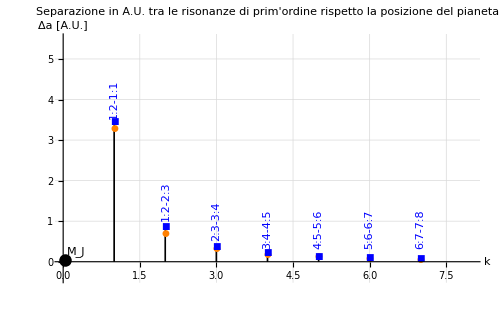

```mathematica
(*
   * Author: Panichi Federico
* Unit Name:risonanze
   * Unit Type: program.nb
   * Project: Master Thesis
   * Package: none
   * Language: Mathematica 9.0
   * Description: Calculate the resonances distances from the planet and beetwen themselves
   * Invocation: PlotLegends
*)

Needs["PlotLegends`"]
b=5.2;
ListPlot[{Table[b(Abs[((k-1)/k)^(2/3)-(k/(k+1))^(2/3)]),{k,1,7,1}],Table[(2 b)/(3 k^2),{k,1,7,1}]},Filling->Axis,PlotRange->{{0,8},{-0.4,5.5}},PlotMarkers->Automatic,PlotStyle->{Orange,Blue},Filling->Axis,FillingStyle->{Black},ImageSize->500,AxesLabel->{"k","Δa [A.U.]"},GridLines->{-1,-.5,.5,1},
Epilog -> {{AbsolutePointSize[9], Black,Text["M_J",{0.25, 0.25}],Point[{0.04,0.04}]},
{Blue,
Text["1:2-1:1",{1, 4},Automatic,{0,1}],
Text["1:2-2:3",{2, 1.5},Automatic,{0,1}],
Text["2:3-3:4",{3,  1},Automatic,{0,1}],
Text["3:4-4:5",{4,  .8},Automatic,{0,1}],
Text["4:5-5:6",{5,  .8},Automatic,{0,1}],
Text["5:6-6:7",{6,  .8},Automatic,{0,1}],
Text["6:7-7:8",{7,  .8},Automatic,{0,1}]}},
PlotLegend->{Style["Δa ≈ (2 SubscriptBox[a, J])/(3 SuperscriptBox[k, 2])  per k → ∞",Italic,12],Style[Row[{"Δa = ",Subscript[a, J]|((k-1)/k)^(2/3)-(k/(k+1))^(2/3)|}],Italic,12]},LegendPosition->{0.,0.},LegendSize->{.9,.5},PlotLabel->Style["Separazione in A.U. tra le risonanze di prim'ordine rispetto la posizione del pianeta",Italic,12],
LegendTextSpace->8.5,LegendTextOffset->{-1.,0.2},LegendBorderSpace->0.6, LegendLabel->Style["Metodo aprrossimato ed esatto:",Italic,12]]
```

```mathematica
(*
   * Author: Panichi Federico
* Unit Name:risonanze
   * Unit Type: program.nb
   * Project: Master Thesis
   * Package: none
   * Language: Mathematica 9.0
   * Description: Calculate the resonances position and type, in green a zone in which the motion is chaotic
   * Invocation: PlotLegends
*)

Needs["PlotLegends`"]
omega[a_]:=2 Pi/a^(3/2);
b=5.2;
s=1.05;
Subscript[R, H]=5.2*(0.001/3.003)^(1/3);
i=Show[
ListPlot[Table[{a/.FindRoot[omega[a]/omega[5.2]==j/(j+1),{a,1}],1},{j,1,9}],Filling->Axis,PlotRange->{{5.,8.5},{0,1.1}},PlotMarkers->None,PlotStyle->Black,Filling->Axis,FillingStyle->{Red},
Epilog ->{{AbsolutePointSize[8], Black,Text["M_J",{5.2, 0.1}],Point[{5.2,0.01}]},
{Red,
Text[Style["1:2",Background->Yellow,Medium,Bold,Black],{5.1,1.0}],
Text[Style["3:4",Background->Green,Medium,Bold,Black],{5.1,.9}],
Text[Style["4:5",Background->Green,Medium,Bold,Black],{5.1,.85}],
Text[Style["5:6",Background->Green,Medium,Bold,Black],{5.1,.8}],
Text[Style["6:7",Background->Green,Medium,Bold,Black],{5.1,.75}],
Text[Style["7:8",Background->Green,Medium,Bold,Black],{5.1,.7}],
Text[Style["8:9",Background->Green,Medium,Bold,Black],{5.1,.65}],
Text[Style["9:10",Background->Green,Medium,Bold,Black],{5.1,.6}],
            Text[Style["2:3",Background->Yellow,Medium,Bold,Black],{5.1,.95}],
Text[Style["R_H",Medium,Italic,Black],{5.2+Subscript[R, H],s}] ,
Text[Style["3.5R_H",Medium,Italic,Black],{5.2+3.5 Subscript[R, H],s}]  } }],

Plot[{x,x},{x,5.0,8.6},PlotRange->{{0,8.5},{0.,1.1}},PlotStyle->{{Red,Thick},{Blue,Thick}},
PlotLegend->{Style["Risonanze 'k:k+1'",Italic,12],Style["Zona caotica",Italic,12]},LegendPosition->{7,.4},LegendSize->{.7,.2},LegendTextSpace->8.5,LegendBorderSpace->.2,LegendLabel->None],

Graphics[{
{Opacity[0.4],Green,Rectangle[{5.2+Subscript[R, H],0.0},{5.2+3.5 Subscript[R, H],1.02}]},
  {Dashed,
Line[{{5.2,1.0},{a/.FindRoot[omega[a]/omega[5.2]==1/2,{a,1}],1.0}}],
Line[{{5.2,.95},{a/.FindRoot[omega[a]/omega[5.2]==2/3,{a,1}],.95}}],
Line[{{5.2,.9},{a/.FindRoot[omega[a]/omega[5.2]==3/4,{a,1}],.9}}],
Line[{{5.2,.85},{a/.FindRoot[omega[a]/omega[5.2]==4/5,{a,1}],.85}}],
Line[{{5.2,.8},{a/.FindRoot[omega[a]/omega[5.2]==5/6,{a,1}],.8}}],
Line[{{5.2,.75},{a/.FindRoot[omega[a]/omega[5.2]==6/7,{a,1}],.75}}],
Line[{{5.2,.7},{a/.FindRoot[omega[a]/omega[5.2]==7/8,{a,1}],.7}}],
Line[{{5.2,.65},{a/.FindRoot[omega[a]/omega[5.2]==8/9,{a,1}],.65}}],
Line[{{5.2,.6},{a/.FindRoot[omega[a]/omega[5.2]==9/10,{a,1}],.6}}] },
{Thick,Blue,
Line[{{5.2+Subscript[R, H],0.0},{5.2+Subscript[R, H],1.02}}],Line[{{5.2+3.5 Subscript[R, H],0.0},{5.2+3.5 Subscript[R, H],1.02}}] },
{Thin,Line[{{5.2,0.0},{5.2,1.02}}] }
},
Frame->True,PlotRange->{{5.,8.5},{0,1.1}},AspectRatio->1],
ImageSize->700]
Export["overlapping.jpg",i]
```

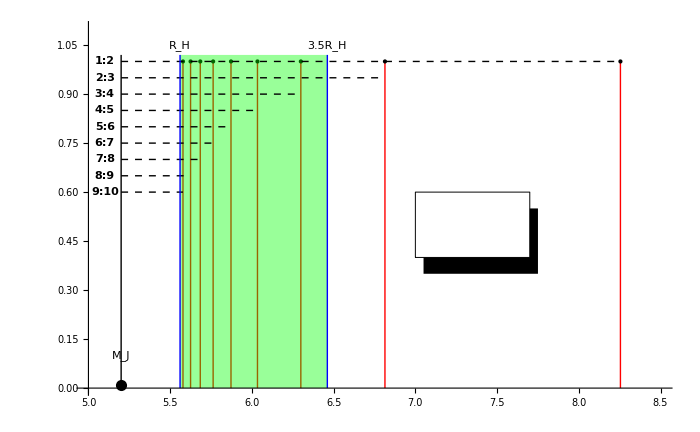

overlapping.jpg

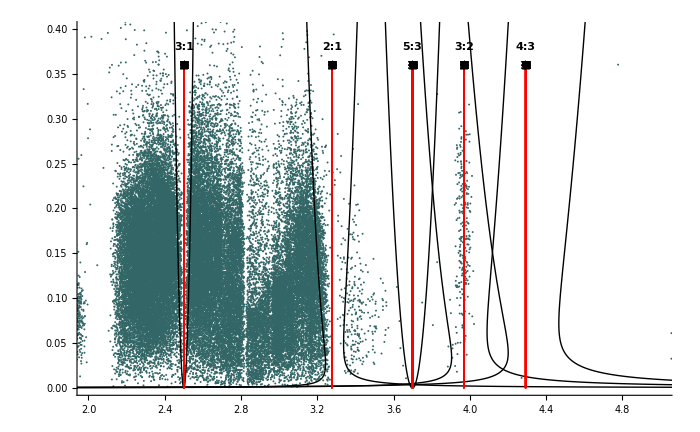

```mathematica
(*
   * Author: Panichi Federico
* Unit Name:risonanze
   * Unit Type: program.nb
   * Project: Master Thesis
   * Package: none
   * Language: Mathematica 9.0
   * Description: Calculate the resonances libration width and overplot it with real asteroids from Main Belt 
   * Invocation: PlotLegends, AstronomicalData
*)

Needs["PlotLegends`"]

omega[a_]:=2 Pi/a^(3/2);
{val1}=FindRoot[omega[a]/omega[5.2]==2,{a,1}] ;
{val2}=FindRoot[omega[a]/omega[5.2]==3,{a,1}];
{val3}=FindRoot[omega[a]/omega[5.2]==5/3,{a,1}];
{val4}=FindRoot[omega[a]/omega[5.2]==3/2,{a,1}];
{val5}=FindRoot[omega[a]/omega[5.2]==4/3,{a,1}];
j=-1;

a21=3.275794729726671;
a31=2.49999;
a53=3.6991708;
a32=3.9683436;
a43=4.2925064;
alfaF21=0.749964;
alfaF31=0.287852;
alfaF53=2.32892;
alfaF32=1.54553;
alfaF43=2.34472;
mu=10^-3;
tot1=alfaF21*mu;
tot2=alfaF31*mu;
tot3=alfaF53*mu;
tot4=alfaF32*mu;
tot5=alfaF43*mu;
d=0.38;
n=0.36;
r=Show[
ParametricPlot[{a21(√((16tot1*x)/3)√(1+tot1/(27 x^3))-(2 tot1)/(9j*x))+a21 ,x},{x,0.00001,1},PlotRange->{{2., 4.7},{0,n}},AxesLabel->{"x","y"},AspectRatio->Automatic,PlotStyle->{Black,Thick} ],
ParametricPlot[{a21(-√((16tot1*x)/3)√(1+tot1/(27 x^3))-(2 tot1)/(9j*x))+a21 ,x},{x,0.00001,1},PlotRange->{{2., 4.7},{0,n}},AxesLabel->{"x","y"},AspectRatio->Automatic,PlotStyle->{Black,Thick}],
ParametricPlot[{2(-√((16tot2*x)/3))+a31 ,x},{x,0.00001,1},PlotRange->{{2., 4.7},{0,n}},AxesLabel->{"x","y"},AspectRatio->Automatic,PlotStyle->{Black,Thick} ],
ParametricPlot[{2(√((16tot2*x)/3))+a31 ,x},{x,0.00001,1},PlotRange->{{2., 4.7},{0,n}},AxesLabel->{"x","y"},AspectRatio->Automatic,PlotStyle->{Black,Thick}],ParametricPlot[{2(-√((16tot3*x)/3))+a53 ,x},{x,0.00001,1},PlotRange->{{2, 5.},{0,n}},AxesLabel->{"x","y"},AspectRatio->Automatic,PlotStyle->{Black,Thick} ],
ParametricPlot[{2(√((16tot3*x)/3))+a53 ,x},{x,0.00001,1},PlotRange->{{2, 5.},{0,n}},AxesLabel->{"x","y"},AspectRatio->Automatic,PlotStyle->{Black,Thick}],ParametricPlot[{a32(-√((16tot4*x)/3(1+tot4/(27 x^3)))-(2 tot4)/(9j*x))+a32 ,x},{x,0.00001,1},PlotRange->{{2, 5.},{0,n}},AxesLabel->{"x","y"},AspectRatio->Automatic,PlotStyle->{Black,Thick} ],
ParametricPlot[{a32(√((16tot4*x)/3(1+tot4/(27 x^3)))-(2 tot4)/(9j*x))+a32 ,x},{x,0.00001,1},PlotRange->{{2, 5.},{0,n}},AxesLabel->{"x","y"},AspectRatio->Automatic,PlotStyle->{Black,Thick}],
ParametricPlot[{a43(-√((16tot5*x)/3(1+tot5/(27 x^3)))-(2 tot5)/(9j*x))+a43 ,x},{x,0.00001,1},PlotRange->{{2, 5.},{0,n}},AxesLabel->{"x","y"},AspectRatio->Automatic,PlotStyle->{Black,Thick} ],
ParametricPlot[{a43(√((16tot5*x)/3(1+tot5/(27 x^3)))-(2 tot5)/(9j*x))+a43 ,x},{x,0.00001,1},PlotRange->{{2, 5.},{0,n}},AxesLabel->{"x","y"},AspectRatio->Automatic,PlotStyle->{Black,Thick}]];


p=ListPlot[Flatten[Table[{
{a/.FindRoot[omega[a]/omega[5.2]==2,{a,1}],n},
{a/.FindRoot[omega[a]/omega[5.2]==3,{a,1}],n},
{a/.FindRoot[omega[a]/omega[5.2]==5/3,{a,1}],n},
{a/.FindRoot[omega[a]/omega[5.2]==3/2,{a,1}],n},
{a/.FindRoot[omega[a]/omega[5.2]==4/3,{a,1}],n}},
{j,1,9,1},{i,2,4,1}],1],
Filling->Axis,FillingStyle->{Red},PlotRange->{{2., 5.},{0,0.4}},PlotMarkers->Automatic,PlotStyle->Black,ImageSize->700];

m=ListPlot[{AstronomicalData[#,"SemimajorAxis"]/149597870691,AstronomicalData[#,"Eccentricity"]}&/@AstronomicalData["MinorPlanet"],PlotStyle->{RGBColor[0.2,0.4,0.4],PointSize[0.002]},PlotRange->{{2., 5.},{0,.4}},Epilog -> 
{Red,
Text[Style["2:1",Background->Yellow,Medium,Bold,Black],{a/.val1, d}],
Text[Style["3:1",Background->Yellow,Medium,Bold,Black],{a/.val2, d}],
Text[Style["5:3",Background->Yellow,Medium,Bold,Black],{a/.val3,  d}],
Text[Style["3:2",Background->Yellow,Medium,Bold,Black],{a/.val4,  d}],
Text[Style["4:3",Background->Yellow,Medium,Bold,Black],{a/.val5,  d}]}];

n=Show[m,r,p,ImageSize->700]
```